# B27

## Error Functions

Units in VOLTS

```mathematica
errorVolt[reading_,range_]:=0.025*Abs[reading]+If[range=="1V",0.006*1,If[range=="10V",0.005*10,If[range=="100V",0.005*100]]]
```

Units in mA

```mathematica
errorCurrent[reading_,range_]:= 0.05*Abs[reading]+If[range=="10mA",0.015*10]
```

## 2.1

```mathematica
xdata21={-13.482,-12.212,-10.4940,-9.0400,-7.5012,-6.0031,-4.5000,-2.9997,-1.5080,0.1990,0.39823,0.60783,0.70160,0.80263,0.90055,1.00591,1.10060,1.21600,1.25610,-15.017}
ydata21={-0.0179,-0.0157,-0.0127,-0.0104,-0.0082,-0.0061,-0.0044,-0.0030,-0.0020,0.1739,1.2045,2.9011,3.8000,4.8051,5.8540,7.0098,8.1145,9.4780,9.9692,-0.0208}
measurementRange21=Join@@{ConstantArray[{"100V","10mA"},2],ConstantArray[{"10V","10mA"},7],ConstantArray[{"1V","10mA"},7],ConstantArray[{"10V","10mA"},3],{{"100V","10mA"}}};
measurementRangeX21=measurementRange21[[All,1]]
```

{-13.482,-12.212,-10.494,-9.04,-7.5012,-6.0031,-4.5,-2.9997,-1.508,0.199,0.39823,0.60783,0.7016,0.80263,0.90055,1.00591,1.1006,1.216,1.2561,-15.017}

{-0.0179,-0.0157,-0.0127,-0.0104,-0.0082,-0.0061,-0.0044,-0.003,-0.002,0.1739,1.2045,2.9011,3.8,4.8051,5.854,7.0098,8.1145,9.478,9.9692,-0.0208}

{100V,100V,10V,10V,10V,10V,10V,10V,10V,1V,1V,1V,1V,1V,1V,1V,10V,10V,10V,100V}

```mathematica
Length/@{xdata21,ydata21,measurementRangeX21}
```

{20,20,20}

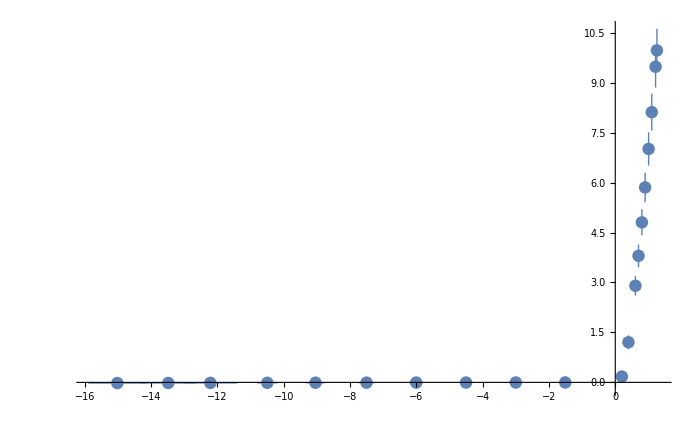

```mathematica
ListPlot[Transpose[{Table[Around[xdata21[[i]],errorVolt[xdata21[[i]],measurementRangeX21[[i]]]],{i,1,Length[xdata21]}],Around[#,errorCurrent[#,"10mA"]]&/@ydata21}]]
```

```mathematica
Sort@Table[Around[xdata21[[i]],errorVolt[xdata21[[i]],measurementRangeX21[[i]]]],{i,1,Length[xdata21]}]
```

{-15.00.9,-13.50.8,-12.20.8,-10.490.31,-9.040.28,-7.500.24,-6.000.20,-4.500.16,-3.000.12,-1.510.09,0.1990.011,0.3980.016,0.6080.021,0.7020.024,0.8030.026,0.9010.029,1.0060.031,1.100.08,1.220.08,1.260.08}

```mathematica
data21=SortBy[Transpose[{Table[Around[xdata21[[i]],errorVolt[xdata21[[i]],measurementRangeX21[[i]]]],{i,1,Length[xdata21]}],Around[#,errorCurrent[#,"10mA"]]&/@ydata21,measurementRangeX21}],First]
```

{{-15.00.9,-0.020.15,100V},{-13.50.8,-0.020.15,100V},{-12.20.8,-0.020.15,100V},{-10.490.31,-0.010.15,10V},{-9.040.28,-0.010.15,10V},{-7.500.24,0.000.15,10V},{-6.000.20,0.000.15,10V},{-4.500.16,0.000.15,10V},{-3.000.12,0.000.15,10V},{-1.510.09,0.000.15,10V},{0.1990.011,0.170.16,1V},{0.3980.016,1.200.21,1V},{0.6080.021,2.900.30,1V},{0.7020.024,3.800.34,1V},{0.8030.026,4.80.4,1V},{0.9010.029,5.90.4,1V},{1.0060.031,7.00.5,1V},{1.100.08,8.10.6,10V},{1.220.08,9.50.6,10V},{1.260.08,10.00.6,10V}}

```mathematica
data21cut=data21[[12;;]]
```

{{0.3980.016,1.200.21,1V},{0.6080.021,2.900.30,1V},{0.7020.024,3.800.34,1V},{0.8030.026,4.80.4,1V},{0.9010.029,5.90.4,1V},{1.0060.031,7.00.5,1V},{1.100.08,8.10.6,10V},{1.220.08,9.50.6,10V},{1.260.08,10.00.6,10V}}

```mathematica
R21={#[[1]],#[[1]]/#[[2]]*10^(3)}&/@data21cut
```

{{0.3980.016,331.59.},{0.6080.021,210.23.},{0.7020.024,185.18.},{0.8030.026,167.15.},{0.9010.029,154.13.},{1.0060.031,144.11.},{1.100.08,136.13.},{1.220.08,128.12.},{1.260.08,126.12.}}

```mathematica
dr21=Table[{(data21cut[[i+2,1]]+data21cut[[i,1]])/2,(data21cut[[i+2,1]]-data21cut[[i,1]])/(data21cut[[i+2,2]]-data21cut[[i,2]])*10^3},{i,1,Length[data21cut]-2}]
```

{{0.5500.014,117.21.},{0.7050.017,102.32.},{0.8010.018,97.32.},{0.9040.020,92.32.},{1.000.04,88.46.},{1.110.04,85.45.},{1.180.06,84.72.}}

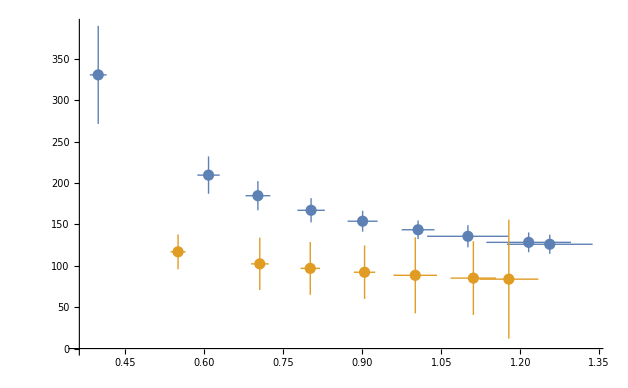

```mathematica
ListPlot[{R21,dr21}]
```

```mathematica
R21[[-1,2,1]]
```

125.998

```mathematica
{#[[1]]*100,#[[2,1]]*10/16,#[[2,2]]*10/16}&/@R21
```

{{39.81.6,206.637,37.003},{60.82.1,130.948,14.0791},{70.22.4,115.395,11.0269},{80.32.6,104.398,9.13161},{90.12.9,96.1469,7.88254},{100.63.1,89.6878,6.97987},{110.8.,84.7711,8.3277},{122.8.,80.1857,7.48125},{126.8.,78.7488,7.23067}}

```mathematica
58+28
96-11
```

86

85

```mathematica
{#[[1]]*100,#[[2]]*10/16}&/@dr21
```

{{55.01.4,73.13.},{70.51.7,64.20.},{80.11.8,61.20.},{90.42.0,58.20.},{100.4.,55.29.},{111.4.,53.28.},{118.6.,52.45.}}

```mathematica
Range[28]*16
```

{16,32,48,64,80,96,112,128,144,160,176,192,208,224,240,256,272,288,304,320,336,352,368,384,400,416,432,448}

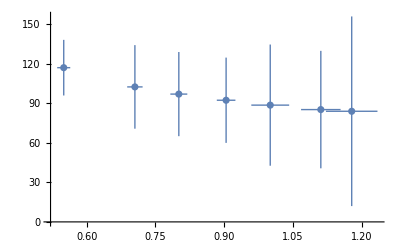

```mathematica
ListPlot[dr21]
```

```mathematica
data21[[1,1]]
```

-15.00.9

```mathematica
data21[[1,2]]
```

-0.020.15

```mathematica
data21[[1,1]]
data21[[1,2]]
data21[[1,1]]/data21[[1,2]]
```

-15.00.9

-0.020.15

0.5.10^3

```mathematica
(data21[[1,1]])/data21[[1,2]]
```

0.5.10^3

```mathematica
{#[[1]],#[[2]],#[[1]]/#[[2]]*10^3}&/@data21//Grid
```

-15.00.9 | -0.020.15 | 0.5.10^6
-13.50.8 | -0.020.15 | 0.6.10^6
-12.20.8 | -0.020.15 | 0.7.10^6
-10.490.31 | -0.010.15 | 0.10.10^6
-9.040.28 | -0.010.15 | 0.01.310^7
-7.500.24 | 0.000.15 | 0.01.710^7
-6.000.20 | 0.000.15 | 0.02.410^7
-4.500.16 | 0.000.15 | 0.13.510^7
-3.000.12 | 0.000.15 | 0.5.10^7
-1.510.09 | 0.000.15 | 0.6.10^7
0.1990.011 | 0.170.16 | 1.11.010^3
0.3980.016 | 1.200.21 | 331.59.
0.6080.021 | 2.900.30 | 210.23.
0.7020.024 | 3.800.34 | 185.18.
0.8030.026 | 4.80.4 | 167.15.
0.9010.029 | 5.90.4 | 154.13.
1.0060.031 | 7.00.5 | 144.11.
1.100.08 | 8.10.6 | 136.13.
1.220.08 | 9.50.6 | 128.12.
1.260.08 | 10.00.6 | 126.12.

```mathematica
data21[[12]]
```

{0.3980.016,1.200.21,1V}

```mathematica
SortBy[Transpose[{Table[xdata21[[i]],{i,1,Length[xdata21]}],Table[errorVolt[xdata21[[i]],measurementRangeX21[[i]]],{i,1,Length[xdata21]}],ydata21,errorCurrent[#,"10mA"]&/@ydata21,measurementRangeX21}],First]//Grid
```

-15.017 | 0.875425 | -0.0208 | 0.15104 | 100V
-13.482 | 0.83705 | -0.0179 | 0.150895 | 100V
-12.212 | 0.8053 | -0.0157 | 0.150785 | 100V
-10.494 | 0.31235 | -0.0127 | 0.150635 | 10V
-9.04 | 0.276 | -0.0104 | 0.15052 | 10V
-7.5012 | 0.23753 | -0.0082 | 0.15041 | 10V
-6.0031 | 0.200078 | -0.0061 | 0.150305 | 10V
-4.5 | 0.1625 | -0.0044 | 0.15022 | 10V
-2.9997 | 0.124993 | -0.003 | 0.15015 | 10V
-1.508 | 0.0877 | -0.002 | 0.1501 | 10V
0.199 | 0.010975 | 0.1739 | 0.158695 | 1V
0.39823 | 0.0159557 | 1.2045 | 0.210225 | 1V
0.60783 | 0.0211958 | 2.9011 | 0.295055 | 1V
0.7016 | 0.02354 | 3.8 | 0.34 | 1V
0.80263 | 0.0260658 | 4.8051 | 0.390255 | 1V
0.90055 | 0.0285137 | 5.854 | 0.4427 | 1V
1.00591 | 0.0311478 | 7.0098 | 0.50049 | 1V
1.1006 | 0.077515 | 8.1145 | 0.555725 | 10V
1.216 | 0.0804 | 9.478 | 0.6239 | 10V
1.2561 | 0.0814025 | 9.9692 | 0.64846 | 10V

```mathematica
N[data⟦-1,2⟧,10]
```

Part::partd: Part specification data⟦-1,2⟧ is longer than depth of object.

data⟦-1,2⟧

```mathematica
SortBy[Transpose[{Table[Around[xdata21[[i]],errorVolt[xdata21[[i]],measurementRangeX21[[i]]]],{i,1,Length[xdata21]}],Around[#,errorCurrent[#,"10mA"]]&/@ydata21,measurementRangeX21}],First]//Grid
```

-15.00.9 | -0.020.15 | 100V
-13.50.8 | -0.020.15 | 100V
-12.20.8 | -0.020.15 | 100V
-10.490.31 | -0.010.15 | 10V
-9.040.28 | -0.010.15 | 10V
-7.500.24 | 0.000.15 | 10V
-6.000.20 | 0.000.15 | 10V
-4.500.16 | 0.000.15 | 10V
-3.000.12 | 0.000.15 | 10V
-1.510.09 | 0.000.15 | 10V
0.1990.011 | 0.170.16 | 1V
0.3980.016 | 1.200.21 | 1V
0.6080.021 | 2.900.30 | 1V
0.7020.024 | 3.800.34 | 1V
0.8030.026 | 4.80.4 | 1V
0.9010.029 | 5.90.4 | 1V
1.0060.031 | 7.00.5 | 1V
1.100.08 | 8.10.6 | 10V
1.220.08 | 9.50.6 | 10V
1.260.08 | 10.00.6 | 10V

```mathematica
SortBy[{-#[[1]]*20/1.5,#[[2]]*10/0.02}&/@SortBy[DeleteCases[Transpose[{Table[Around[xdata21[[i]],errorVolt[xdata21[[i]],measurementRangeX21[[i]]]],{i,1,Length[xdata21]}],Around[#,errorCurrent[#,"10mA"]]&/@ydata21}],x_/;x[[1]]>0],First],First]
```

{{-16.71.1,4985.324.},{-16.21.1,4739.312.},{-14.71.0,4057.278.},{-13.40.4,3505.250.},{-12.00.4,2927.221.},{-10.700.35,2403.195.},{-9.350.31,1900.170.},{-8.100.28,1451.148.},{-5.310.21,602.105.},{-2.650.15,87.79.},{20.11.2,-1.75.},{40.01.7,-2.75.},{60.02.2,-2.75.},{80.02.7,-3.75.},{100.03.2,-4.75.},{121.4.,-5.75.},{140.4.,-6.75.},{163.11.,-8.75.},{180.11.,-9.75.},{200.12.,-10.76.}}

```mathematica
NumberForm[-15.020.12,10]
```

-15.020.12

```mathematica
regression={#[[1,1]],#[[2,1]]}&/@data21[[-8;;-1,{1,2}]]
```

{{0.60783,2.9011},{0.7016,3.8},{0.80263,4.8051},{0.90055,5.854},{1.00591,7.0098},{1.1006,8.1145},{1.216,9.478},{1.2561,9.9692}}

```mathematica
LinearModelFit[regression,x,x]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -3.90863 | 0.167103 | -23.3906 | 4.00516×10^-7
x | 10.9601 | 0.171483 | 63.9138 | 9.86423×10^-10

```mathematica
LinearModelFit[regression,x,x]["RSquared"]
```

0.998533

```mathematica
DeleteCases[data21,x_/;x[[1,1]]<0]
```

{{0.1990.011,0.170.16,1V},{0.3980.016,1.200.21,1V},{0.6080.021,2.900.30,1V},{0.7020.024,3.800.34,1V},{0.8030.026,4.80.4,1V},{0.9010.029,5.90.4,1V},{1.0060.031,7.00.5,1V},{1.100.08,8.10.6,10V},{1.220.08,9.50.6,10V},{1.260.08,10.00.6,10V}}

```mathematica
{#[[1]]*100,#[[2]]*20}&/@DeleteCases[data21,x_/;x[[1,1]]<0]
```

{{19.91.1,3.53.2},{39.81.6,24.4.},{60.82.1,58.6.},{70.22.4,76.7.},{80.32.6,96.8.},{90.12.9,117.9.},{100.63.1,140.10.},{110.8.,162.11.},{122.8.,190.12.},{126.8.,199.13.}}

## 2.2

```mathematica
xdata22={0.08775,0.10780,0.19150,0.40583,0.46618,0.58712,0.61722,0.64693,0.70046,0.71934,0.76200,0.78893};
ydata22={0,0.0001,0.0001,0.0145,0.0713,1.0351,1.6921,2.6183,4.9500,5.9551,8.0510,10.2594};
```

```mathematica
Length/@{xdata22,ydata22}
```

{12,12}

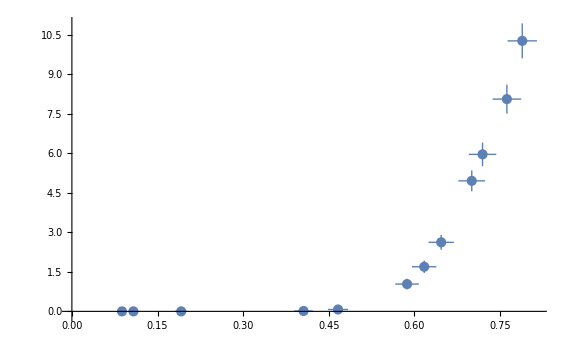

```mathematica
ListPlot[Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata22,Around[#,errorCurrent[#,"10mA"]]&/@ydata22}]]
```

```mathematica
Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata22,Around[#,errorCurrent[#,"10mA"]]&/@ydata22}]
```

{{0.0880.008,0.000.15},{0.1080.009,0.000.15},{0.1920.011,0.000.15},{0.4060.016,0.010.15},{0.4660.018,0.070.15},{0.5870.021,1.040.20},{0.6170.021,1.690.23},{0.6470.022,2.620.28},{0.7000.024,5.00.4},{0.7190.024,6.00.4},{0.7620.025,8.10.6},{0.7890.026,10.30.7}}

```mathematica
LinearModelFit[Transpose[{xdata22,ydata22}][[-5;;-1]],x,x]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -31.723 | 2.61982 | -12.1088 | 0.00121228
x | 52.6441 | 3.61249 | 14.5728 | 0.000700692

```mathematica
LinearModelFit[Transpose[{xdata22,ydata22}][[-5;;-1]],x,x]["RSquared"]
```

0.98607

## 2.3

```mathematica
xdata23=-{1.0874,2.0561,3.0324,4.0110,5.0578,6.0195,7.0213,8.0220,9.0431,11.901,12.016,11.953,12.124};
ydata23=-Join@@{ConstantArray[0,9],{0.7765,5.7150,2.8108,10.6471}};
measurementRange23=Join@@{ConstantArray["10V",10],ConstantArray["100V",3]};
```

```mathematica
Length/@{xdata23,ydata23,measurementRange23}
```

{13,13,13}

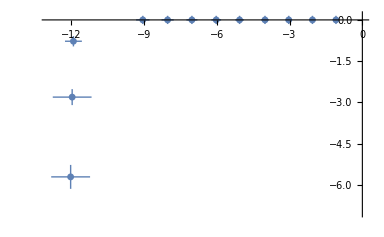

```mathematica
ListPlot[Transpose[{Table[Around[xdata23[[i]],errorVolt[xdata23[[i]],measurementRange23[[i]]]],{i,1,Length[xdata23]}],Around[#,errorCurrent[#,"10mA"]]&/@ydata23}]]
```

```mathematica
xdata23pt2={0.01182,0.40023,0.68661,0.74500,0.80032,0.82443,0.85063,0.90308};
ydata23pt2={0,0.0001,0.6014,1.8823,4.1736,5.4504,6.9884,10.4746};
```

```mathematica
Length/@{xdata23pt2,ydata23pt2}
```

{8,8}

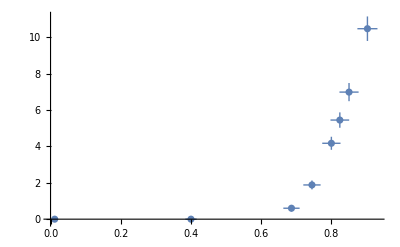

```mathematica
ListPlot[Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata23pt2,Around[#,errorCurrent[#,"10mA"]]&/@ydata23pt2}]]
```

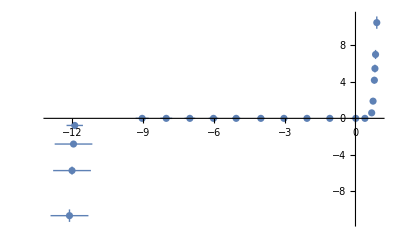

```mathematica
ListPlot[Join[Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata23pt2,Around[#,errorCurrent[#,"10mA"]]&/@ydata23pt2}],Transpose[{Table[Around[xdata23[[i]],errorVolt[xdata23[[i]],measurementRange23[[i]]]],{i,1,Length[xdata23]}],Around[#,errorCurrent[#,"10mA"]]&/@ydata23}]]]
```

```mathematica
SortBy[Join[Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata23pt2,Around[#,errorCurrent[#,"10mA"]]&/@ydata23pt2}],Transpose[{Table[Around[xdata23[[i]],errorVolt[xdata23[[i]],measurementRange23[[i]]]],{i,1,Length[xdata23]}],Around[#,errorCurrent[#,"10mA"]]&/@ydata23}]],First]
```

{{-12.10.8,-10.60.7},{-12.00.8,-5.70.4},{-12.00.8,-2.810.29},{-11.900.35,-0.780.19},{-9.040.28,0.000.15},{-8.020.25,0.000.15},{-7.020.23,0.000.15},{-6.020.20,0.000.15},{-5.060.18,0.000.15},{-4.010.15,0.000.15},{-3.030.13,0.000.15},{-2.060.10,0.000.15},{-1.090.08,0.000.15},{0.0120.006,0.000.15},{0.4000.016,0.000.15},{0.6870.023,0.600.18},{0.7450.025,1.880.24},{0.8000.026,4.20.4},{0.8240.027,5.50.4},{0.8510.027,7.00.5},{0.9030.029,10.50.7}}

```mathematica
xdata23pt2
```

{0.01182,0.40023,0.68661,0.745,0.80032,0.82443,0.85063,0.90308}

```mathematica
ydata23pt2
```

{0,0.0001,0.6014,1.8823,4.1736,5.4504,6.9884,10.4746}

```mathematica
LinearModelFit[Transpose[{xdata23pt2,ydata23pt2}][[-4;;-1]],x,x]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -45.3725 | 1.86931 | -24.2723 | 0.00169306
x | 61.7373 | 2.21095 | 27.9234 | 0.00128006

```mathematica
ydata23
```

{0,0,0,0,0,0,0,0,0,-0.7765,-5.715,-2.8108,-10.6471}

## 2.4

```mathematica
xdata24={3.0137,6.0058,9.0123,12.013,15.030,18.048,21.051,24.015,27.029,30.015}
ydata24={3.0124,6.0033,9.0089,11.889,11.891,11.910,11.926,11.944,11.961,11.977}
measurementRange24=Join@@{ConstantArray["10V",3],ConstantArray["100V",7]}
```

{3.0137,6.0058,9.0123,12.013,15.03,18.048,21.051,24.015,27.029,30.015}

{3.0124,6.0033,9.0089,11.889,11.891,11.91,11.926,11.944,11.961,11.977}

{10V,10V,10V,100V,100V,100V,100V,100V,100V,100V}

```mathematica
Length/@{xdata24,ydata24,measurementRange24}
```

{10,10,10}

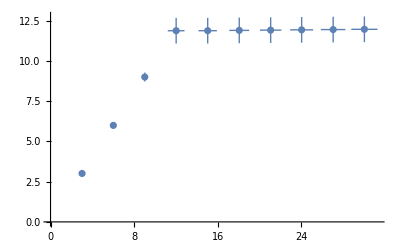

```mathematica
ListPlot[Transpose[{Table[Around[xdata24[[i]],errorVolt[xdata24[[i]],measurementRange24[[i]]]],{i,1,Length[xdata24]}],Table[Around[ydata24[[i]],errorVolt[ydata24[[i]],measurementRange24[[i]]]],{i,1,Length[xdata24]}]}]]
```

```mathematica
Transpose[{Table[Around[xdata24[[i]],errorVolt[xdata24[[i]],measurementRange24[[i]]]],{i,1,Length[xdata24]}],Table[Around[ydata24[[i]],errorVolt[ydata24[[i]],measurementRange24[[i]]]],{i,1,Length[xdata24]}]}]
```

{{3.010.13,3.010.13},{6.010.20,6.000.20},{9.010.28,9.010.28},{12.00.8,11.90.8},{15.00.9,11.90.8},{18.01.0,11.90.8},{21.11.0,11.90.8},{24.01.1,11.90.8},{27.01.2,12.00.8},{30.01.3,12.00.8}}

## 2.5

```mathematica
xdata25={0.2040,0.4074,0.6037,0.8265,1.0228,1.2000,1.5030,1.5864,1.6512,1.7038,1.7484,1.8073,1.8526,1.9005,1.9545,2.0000};
ydata25=Join@@{ConstantArray[0,7],{0.0054,0.0223,0.0805,0.2035,0.6457,1.4831,3.0669,5.6934,8.4215}}
```

{0,0,0,0,0,0,0,0.0054,0.0223,0.0805,0.2035,0.6457,1.4831,3.0669,5.6934,8.4215}

```mathematica
Length/@{xdata25,ydata25}
```

{16,16}

```mathematica
errorVolt[0,"10mA"]
```

0.+Null

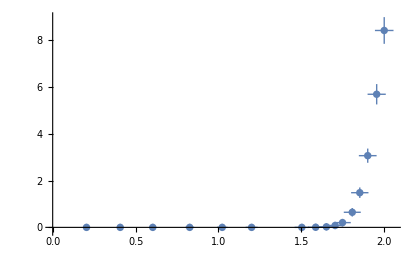

```mathematica
ListPlot[Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata25,Around[#,errorCurrent[#,"10mA"]]&/@ydata25}]]
```

```mathematica
Transpose[{Around[#,errorVolt[#,"1V"]]&/@xdata25,Around[#,errorCurrent[#,"10mA"]]&/@ydata25}]
```

{{0.2040.011,0.000.15},{0.4070.016,0.000.15},{0.6040.021,0.000.15},{0.8270.027,0.000.15},{1.0230.032,0.000.15},{1.200.04,0.000.15},{1.500.04,0.000.15},{1.590.05,0.000.15},{1.650.05,0.020.15},{1.700.05,0.080.15},{1.750.05,0.200.16},{1.810.05,0.650.18},{1.850.05,1.480.22},{1.900.05,3.070.30},{1.950.05,5.70.4},{2.000.06,8.40.6}}

```mathematica
1
```

1